# Normal Wheel

```mathematica
leftcenter={-1.25,0};
rightcenter={1.25,0};
innerradius=0.65;
size=1;

rimthickness=0.005;

(* Current tested offsets: 0.95 - 0.2 - 0.3 *)
color="Grayscale";
inneroffset=0;
wheeloffset=0.25;
outeroffset=0.5;
saturation=1;
```

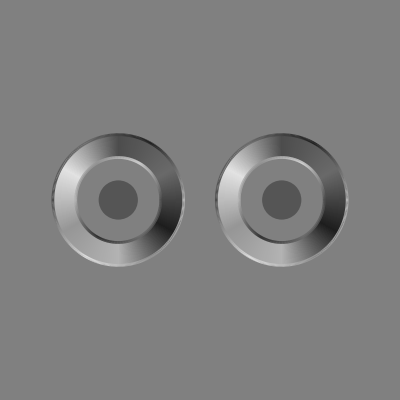

```mathematica
wheel1=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-wheeloffset,saturation],color],Disk[leftcenter,size,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]];
wheel2=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-wheeloffset,saturation],color],Disk[rightcenter,size,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]];
outeroutline1=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[rimthickness],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-outeroffset,saturation],color],Circle[leftcenter,size,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]];
outeroutline2=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[rimthickness],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-outeroffset,saturation],color],Circle[rightcenter,size,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]];
inneroutline1=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[rimthickness],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-inneroffset,saturation],color],Circle[leftcenter,innerradius,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]];
inneroutline2=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[rimthickness],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-inneroffset,saturation],color],Circle[rightcenter,innerradius,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]];
cutout1=Graphics[{Gray,Disk[leftcenter,innerradius]}];
cutout2=Graphics[{Gray,Disk[rightcenter,innerradius]}];
ctrcircle1=Graphics[{Darker[Gray],Disk[leftcenter,0.3]}];
ctrcircle2=Graphics[{Darker[Gray],Disk[rightcenter,0.3]}];
Show[
ParametricPlot[t,{t,-10,10},PlotRange->{-2.5,2.5},Background->Gray,PlotStyle->Gray,Axes->False],
(*Graphics[Raster[ImageData[wheelimg],{{leftcenter[[1]]-size,size},{leftcenter[[1]]+size,-size}}]],
Graphics[Raster[ImageData[wheelimg],{{rightcenter[[1]]-size,size},{rightcenter[[1]]+size,-size}}]],*)
Graphics[First@wheel1],
Graphics[First@wheel2],
cutout1,
cutout2,
Graphics[First@outeroutline1],
Graphics[First@inneroutline1],
Graphics[First@outeroutline2],
Graphics[First@inneroutline2],
ctrcircle1,
ctrcircle2
]
```

```mathematica
Export["C://Users/Hong/Downloads/grayscale.png",
Show[
ParametricPlot[t,{t,-10,10},PlotRange->{-2.5,2.5},Background->Gray,PlotStyle->Gray,Axes->False],
Graphics[First@wheel1],
Graphics[First@wheel2],
cutout1,
cutout2,
Graphics[First@outeroutline1],
Graphics[First@inneroutline1],
Graphics[First@outeroutline2],
Graphics[First@inneroutline2],
ctrcircle1,
ctrcircle2
],
ImageSize->1200];
```

```mathematica
slides=Table[
Show[
ParametricPlot[t,{t,-10,10},PlotRange->{-2.5,2.5},Background->Gray,PlotStyle->Gray,Axes->False],
Graphics[Rotate[First@wheel1,θ]],
Graphics[Rotate[First@wheel2,-θ]],
cutout1,
cutout2,
Graphics[Rotate[First@outeroutline1,θ]],
Graphics[Rotate[First@inneroutline1,θ]],
Graphics[Rotate[First@outeroutline2,-θ]],
Graphics[Rotate[First@inneroutline2,-θ]],
ctrcircle1,
ctrcircle2
],
{θ,0,2π,π/50}
];
Export["C://Users/Hong/Documents/test.avi",slides,ImageResolution->1200,Antialiasing->True];
```

# Checkered Fan

```mathematica
fanimg=Import["C:\\Users\\Hong\\Downloads\\fan_blurred.png"];
leftcenter={-1.25,0};
rightcenter={1.25,0};
innerradius=0.7;
wheelradius=0.85;
outerradius=1;
```

```mathematica
cutout1=Graphics[{Gray,Disk[leftcenter,innerradius]}];
cutout2=Graphics[{Gray,Disk[rightcenter,innerradius]}];
ctrcircle1=Graphics[{Darker[Gray],Disk[leftcenter,0.3]}];
ctrcircle2=Graphics[{Darker[Gray],Disk[rightcenter,0.3]}];
Show[
ParametricPlot[t,{t,-10,10},PlotRange->{-2.5,2.5},Background->Gray,PlotStyle->Gray,Axes->False],
Graphics[Rotate[Raster[ImageData[fanimg],{{leftcenter[[1]]-outerradius,outerradius},{leftcenter[[1]]+outerradius,-outerradius}}],π/16]],
Graphics[Rotate[Raster[ImageData[fanimg],{{rightcenter[[1]]-outerradius,outerradius},{rightcenter[[1]]+outerradius,-outerradius}}],π/16]],
Graphics[Raster[ImageData[fanimg],{{leftcenter[[1]]-wheelradius,wheelradius},{leftcenter[[1]]+wheelradius,-wheelradius}}]],
Graphics[Raster[ImageData[fanimg],{{rightcenter[[1]]-wheelradius,wheelradius},{rightcenter[[1]]+wheelradius,-wheelradius}}]],
cutout1,
cutout2,
ctrcircle1,
ctrcircle2
]
```

-Graphics-

```mathematica
slides=Table[
Show[
ParametricPlot[t,{t,-10,10},PlotRange->{-2.5,2.5},Background->Gray,PlotStyle->Gray,Axes->False],
Graphics[Rotate[Raster[ImageData[fanimg],{{leftcenter[[1]]-outerradius,outerradius},{leftcenter[[1]]+outerradius,-outerradius}}],π/16+θ]],
Graphics[Rotate[Raster[ImageData[fanimg],{{rightcenter[[1]]-outerradius,outerradius},{rightcenter[[1]]+outerradius,-outerradius}}],π/16-θ]],
Graphics[Rotate[Raster[ImageData[fanimg],{{leftcenter[[1]]-wheelradius,wheelradius},{leftcenter[[1]]+wheelradius,-wheelradius}}],θ]],
Graphics[Rotate[Raster[ImageData[fanimg],{{rightcenter[[1]]-wheelradius,wheelradius},{rightcenter[[1]]+wheelradius,-wheelradius}}],-θ]],
cutout1,
cutout2,
ctrcircle1,
ctrcircle2
],
{θ,0,2π,π/50}
];
Export["C://Users/Hong/Documents/illusions/fan_blurred2.avi",slides,Antialiasing->True];
```

# Concentric Rings

```mathematica
leftcenter={-1.25,0};
rightcenter={1.25,0};
innerradius=0.65;
size=1;

wheeloffset=0.2;
outeroffset=0.3;
inneroffset=0.7;
outerthickness=0.01;
innerthickness=0.01;
```

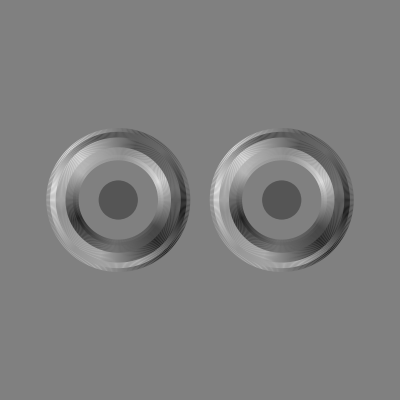

```mathematica
wheel1=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-wheeloffset],"GrayScale"],Disk[leftcenter,size,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]];
wheel2=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-wheeloffset],"GrayScale"],Disk[rightcenter,size,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]];
wheel11=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[0.025],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-0.9],"GrayScale"],Circle[leftcenter,0.7,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]];
wheel22=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[0.025],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-0.9],"GrayScale"],Circle[rightcenter,0.7,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]];
outeroutline1=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[outerthickness],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-outeroffset],"GrayScale"],Circle[leftcenter,1,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]];
outeroutline2=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[outerthickness],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-outeroffset],"Grayscale"],Circle[rightcenter,1,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]];
inneroutline1=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[innerthickness],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-inneroffset],"GrayScale"],Circle[leftcenter,innerradius,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]];
inneroutline2=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[innerthickness],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-inneroffset],"GrayScale"],Circle[rightcenter,innerradius,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]];
cutout1=Graphics[{Gray,Disk[leftcenter,innerradius]}];
cutout2=Graphics[{Gray,Disk[rightcenter,innerradius]}];
ctrcircle1=Graphics[{Darker[Gray],Disk[leftcenter,0.3]}];
ctrcircle2=Graphics[{Darker[Gray],Disk[rightcenter,0.3]}];
Show[
ParametricPlot[t,{t,-10,10},PlotRange->{-2.5,2.5},Background->Gray,PlotStyle->Gray,Axes->False],
Graphics[First@wheel1],
Graphics[First@wheel2],
Graphics[First@wheel11],
Graphics[First@wheel22],
cutout1,
cutout2,
Graphics[First@outeroutline1],
Graphics[First@inneroutline1],
Graphics[First@outeroutline2],
Graphics[First@inneroutline2],
ctrcircle1,
ctrcircle2
]
```

```mathematica
slides=Table[
Show[
ParametricPlot[t,{t,-10,10},PlotRange->{-2.5,2.5},Background->Gray,PlotStyle->Gray,Axes->False],
Graphics[Rotate[First@wheel1,θ]],
Graphics[Rotate[First@wheel2,-θ]],
cutout1,
cutout2,
Graphics[Rotate[First@outeroutline1,θ]],
Graphics[Rotate[First@inneroutline1,θ]],
Graphics[Rotate[First@outeroutline2,-θ]],
Graphics[Rotate[First@inneroutline2,-θ]],
ctrcircle1,
ctrcircle2
],
{θ,0,2π,π/50}
];
Export["C://Users/Hong/Documents/thickrims.avi",slides,ImageResolution->1200,Antialiasing->True];
```

# Arcs and Slices

```mathematica
leftcenter={-1.25,0};
rightcenter={1.25,0};
innerradius=0.65;
size=1;

(* Current tested offsets: 0.95 - 0.2 - 0.3 *)
color="Grayscale";
inneroffset=0.4;
wheeloffset=0.65;
outeroffset=0.8;
saturation=1;
```

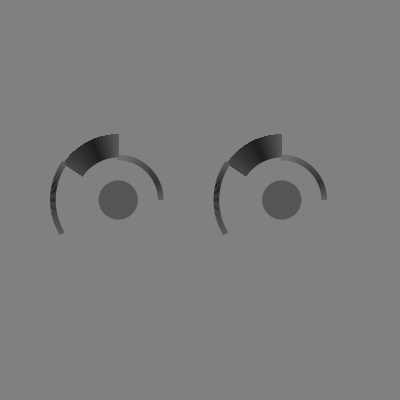

```mathematica
wheel1=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[0.065],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-wheeloffset,saturation],color],Disk[leftcenter,size,{i angle,(i+1) angle}]},{i,90,145}]}]];
wheel2=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[0.065],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-wheeloffset,saturation],color],Disk[rightcenter,size,{i angle,(i+1) angle}]},{i,90,145}]}]];
outeroutline1=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[0.01],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-outeroffset,saturation],color],Circle[leftcenter,size,{i angle,(i+1) angle}]},{i,145,210}]}]];
outeroutline2=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[0.01],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-outeroffset,saturation],color],Circle[rightcenter,size,{i angle,(i+1) angle}]},{i,145,210}]}]];
inneroutline1=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[0.01],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-inneroffset,saturation],color],Circle[leftcenter,innerradius,{i angle,(i+1) angle}]},{i,0,90}]}]];
inneroutline2=With[{sectors=360},angle=2 Pi/sectors;Graphics[{Thickness[0.01],Table[{Antialiasing->False,ColorConvert[Hue[i/sectors-inneroffset,saturation],color],Circle[rightcenter,innerradius,{i angle,(i+1) angle}]},{i,0,90}]}]];
cutout1=Graphics[{Gray,Disk[leftcenter,innerradius]}];
cutout2=Graphics[{Gray,Disk[rightcenter,innerradius]}];
ctrcircle1=Graphics[{Darker[Gray],Disk[leftcenter,0.3]}];
ctrcircle2=Graphics[{Darker[Gray],Disk[rightcenter,0.3]}];
Show[
ParametricPlot[t,{t,-10,10},PlotRange->{-2.5,2.5},Background->Gray,PlotStyle->Gray,Axes->False],
Graphics[First@wheel1],
Graphics[First@wheel2],
cutout1,
cutout2,
Graphics[First@outeroutline1],
Graphics[First@inneroutline1],
Graphics[First@outeroutline2],
Graphics[First@inneroutline2],
ctrcircle1,
ctrcircle2
]
```

```mathematica
slides=Table[
Show[
ParametricPlot[t,{t,-10,10},PlotRange->{-2.5,2.5},Background->Gray,PlotStyle->Gray,Axes->False],
Graphics[Rotate[First@wheel1,θ,leftcenter]],
Graphics[Rotate[First@wheel2,-θ,rightcenter]],
cutout1,
cutout2,
Graphics[Rotate[First@outeroutline1,θ,leftcenter]],
Graphics[Rotate[First@inneroutline1,θ,leftcenter]],
Graphics[Rotate[First@outeroutline2,-θ,rightcenter]],
Graphics[Rotate[First@inneroutline2,-θ,rightcenter]],
ctrcircle1,
ctrcircle2
],
{θ,0,2π,π/50}
];
Export["C://Users/Hong/Documents/slices.avi",slides,ImageResolution->1200,Antialiasing->True];
```